# Combine Plots

```mathematica
ClearAll["Global`*"]
```

## Prerequisites

```mathematica
cleanRegionPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,{__,_Line},Infinity];(*only change*)Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]];
```

```mathematica
myTicks[lower_,upper_,step_]:=Flatten[Module[{Local=#,LocalTicks},LocalTicks=Log[10,Range[10^(#-1),10^#,(10^#-10^(#-1))/(10-1)]];
Join[{#,""}&/@Most[LocalTicks],{{Last[LocalTicks],Which[Last[LocalTicks]==0,1,Last[LocalTicks]==1,10,True,Power[10,ToString[Last[LocalTicks]]]],{0.03,0}(*longer ticks*)}}]]&/@Range[lower,upper,step],1];
```

```mathematica
mh=125.13;
```

## High-T phase transition

```mathematica
DumpGet[NotebookDirectory[]<>"/phase_transition/output/highT.m"]
```

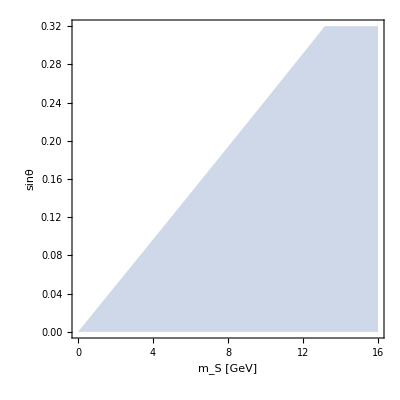

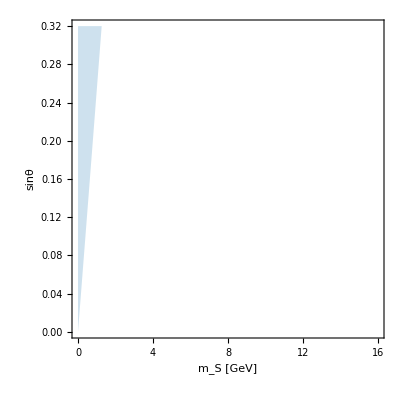

```mathematica
HighT‵SFOPT‵plot=RegionPlot[{strength[mS,sinθ]≤1.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,1],Opacity[0.3]},BoundaryStyle->None,PlotRangePadding->None]//cleanRegionPlot
non‵restore‵plot=RegionPlot[{Positive‵factor[mS,sinθ]≤0.},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,7],Opacity[0.3]},BoundaryStyle->None,PlotRangePadding->None]//cleanRegionPlot
```

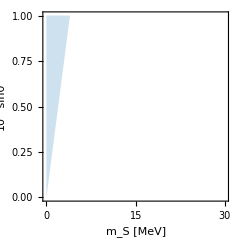

```mathematica
non‵restore‵plot‵smallmS=RegionPlot[{Positive‵factor[mS/1000,sinθ/1000]≤0.},{mS,0,30},{sinθ,0,1},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["10^-3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,7],Opacity[0.3]},BoundaryStyle->None,PlotRangePadding->None]//cleanRegionPlot
```

## LEP bound

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"/probe/LEP1996.csv"];
```

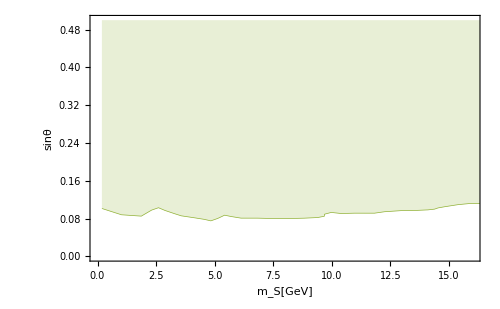

```mathematica
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[ColorData[97,3],Thickness[0.001]],PlotRange->{{0,16},{0,0.5}}]
```

## LHCb

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"probe/LHCb.csv"];
```

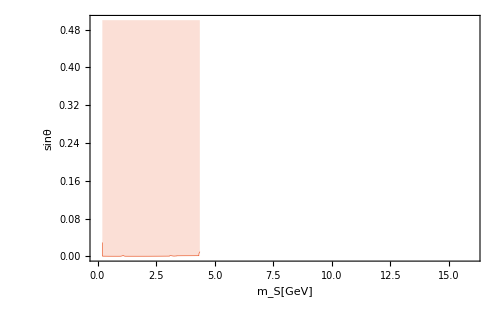

```mathematica
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[ColorData[97,4],Thickness[0.001]],PlotRange->{{0,16},{0,0.5}}]
```

## Vacuum tunneling trajectory

```mathematica
DumpGet[NotebookDirectory[]<>"model_setup/output/V0T_BPeg.m"]
```

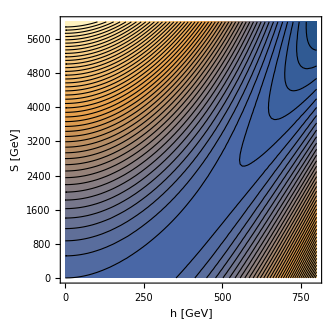

```mathematica
potential=ContourPlot[V0T‵BPeg[h,S],{h,0,800},{S,0,6000},Contours->50,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h [GeV]",FontFamily->"Times",FontSize->18],Style["S [GeV]",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]
```

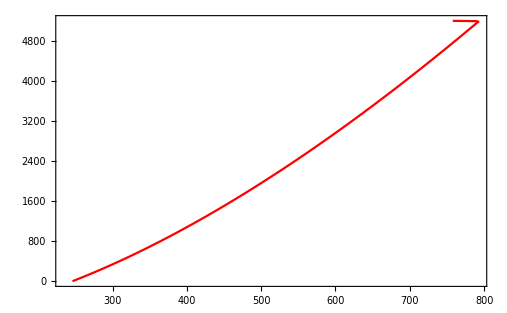

```mathematica
pathdata={100*#2,100*#3}& @@@Import[NotebookDirectory[]<>"model_setup/output/BPeg.csv","Data"][[2;;]];
path=ListLinePlot[pathdata,PlotStyle->Red]
```

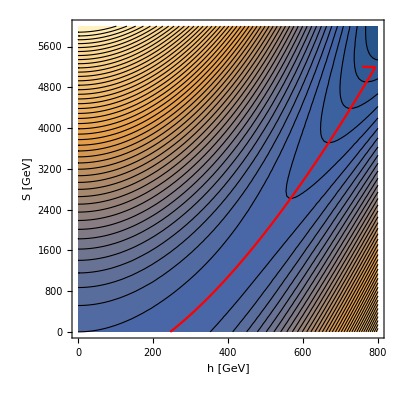

```mathematica
Show[potential,path]
```

```mathematica
potential3d=Plot3D[V0T‵BPeg[h,S],{h,0,800},{S,0,6000}]
```

-Graphics3D-

```mathematica
potential‵data=V0T‵BPeg @@@ pathdata;
trajectorydata=MapThread[Append,{pathdata,potential‵data}];
```

```mathematica
trajectory=ListLinePlot3D[trajectorydata,PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[potential3d,trajectory]
```

-Graphics3D-

## Vacuum tunneling action

```mathematica
actiondata={#1,Log10[#2]}&@@@Import[NotebookDirectory[]<>"model_setup/output/Action_curve.csv"];
```

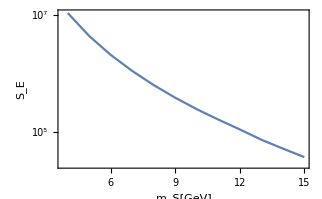

```mathematica
Actionchange=ListLinePlot[actiondata,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["S_E",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18],PlotRangePadding->None,ImageSize->500},FrameTicks->{{myTicks[3,8,1],None},{True,None}}]
```

## Fine-tunning contour

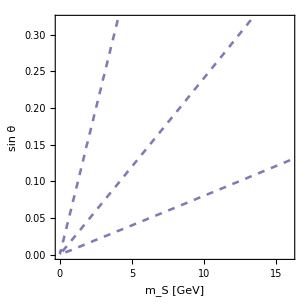

```mathematica
finetuning=ContourPlot[mS^2/(mS^2(1-sinθ^2)+mh^2(sinθ^2)),{mS,0,16},{sinθ,0,0.32},ContourShading->None,Contours->{0.1,0.01,0.5},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ContourStyle->{Directive[Dashed,ColorData[97,5],Thickness[0.006]]}]
```

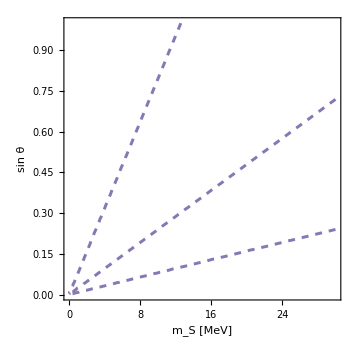

```mathematica
finetuningsmallmS=ContourPlot[(mS/1000)^2/((mS/1000)^2(1-(sin/1000)^2)+mh^2((sin/1000)^2)),{mS,0,30},{sin,0,1},ContourShading->None,Contours->{0.1,0.01,0.5},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [MeV]",FontFamily->"Times",FontSize->18],Style["sin θ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ContourStyle->{Directive[Dashed,ColorData[97,5],Thickness[0.006]]},PlotRangePadding->None]
```

## Kaon Decay

```mathematica
NA621={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-1.csv"];
NA622={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-2.csv"];
NA623={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-3.csv"];
E9491={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949.csv"];
E9492={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949-2.csv"];
```

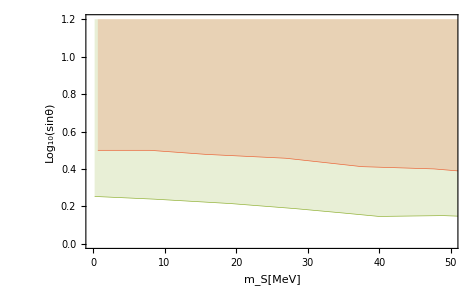

```mathematica
Kaondecay=ListLinePlot[{NA621,E9491},Filling->Top,PlotRange->{{0,50},{0,1.2}},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["Log_10(sinθ)",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{Directive[ColorData[97,3],Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]]}]
```

## CMB

```mathematica
me=5.11*10^-4;
m=1;
GeV=1/(1.97*10^-16*m);
ΓSee[mS_,sinθ_]:=mS/(32π v^2)me^2(1-4 me^2/mS^2)^(3/2)sinθ^2 GeV;
τS[mS_,sinθ_]:=1/ΓSee[mS,sinθ] 1/(3*10^8);
```

```mathematica
Planckdata=Import[NotebookDirectory[]<>"./probe/Planck.csv"];
CMBS4data=Import[NotebookDirectory[]<>"./probe/CMB-S4.csv"];
Planckfunc[mS_]:=Interpolation[Planckdata][mS]
CMBfunc[mS_]:=Interpolation[CMBS4data][mS]
```

```mathematica
τS[0.005,10^-4]
```

5.39057×10^-6 v^2

```mathematica
Min[{#1}&@@@CMBS4data]
```

14.2856

```mathematica
Min[{#1}&@@@Planckdata]
```

3.5771

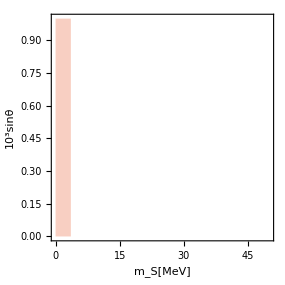

```mathematica
Planck=RegionPlot[mS<=Min[{#1}&@@@Planckdata],{mS,0,50},{s,0,1.},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,4],Opacity[0.3]}]//cleanRegionPlot
```

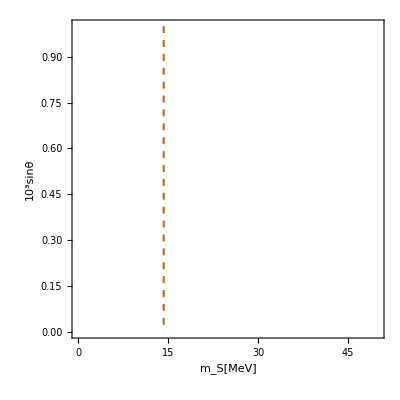

```mathematica
CMB=ContourPlot[mS==Min[{#1}&@@@CMBS4data],{mS,0,50},{s,0,1.},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ContourStyle->{ColorData[97,6],Dashed}]
```

## β/H

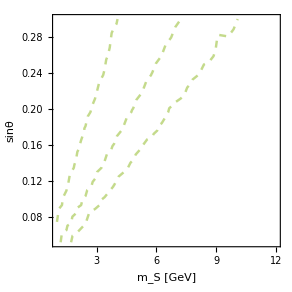

```mathematica
data1d={#1, #2, #4}& @@@Import[NotebookDirectory[]<>"phase_transition/output/scan1d.csv"][[2;;]];
betaH1d=ListContourPlot[data1d,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},Contours->{100000,30000,50000},ContourStyle->Directive[Dashed,ColorData[97,23],Thickness[0.006]]]
```

```mathematica
data2dorigin=Import[NotebookDirectory[]<>"phase_transition/output/scan.csv"];
data2d=Select[data2dorigin,#[[5]]>=0.2 &];
```

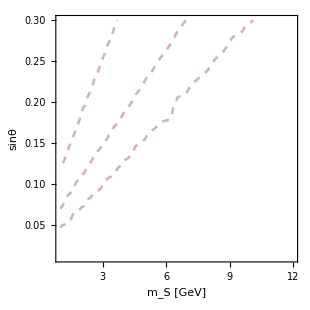

```mathematica
betaH2ddata={#1, #2, #7}& @@@data2d;
betaH2d=ListContourPlot[betaH2ddata,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},Contours->{100000,30000,50000},ContourStyle->Directive[Dashed,ColorData[97,9],Thickness[0.006]]]
```

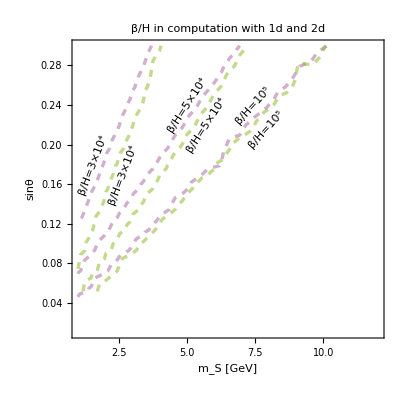

```mathematica
Show[betaH2d,betaH1d,PlotLabel->"β/H in computation with 1d and 2d",Epilog->{Inset[Framed[Column[{LineLegend[{Directive[Dashed,ColorData[97,9],Thickness[0.006]],Directive[Dashed,ColorData[97,23],Thickness[0.006]]},{"2d case","1d case"}]}],RoundingRadius->5],Scaled[{0.8,0.15}]],Inset[Rotate[Framed[Style["β/H=10^5",ColorData[97,9]],FrameStyle->None],48Degree],{7.4,0.24}],Inset[Rotate[Framed[Style["β/H=5×10^4",ColorData[97,9]],FrameStyle->None],57Degree],{5.,0.24}],Inset[Rotate[Framed[Style["β/H=3×10^4",ColorData[97,9]],FrameStyle->None],69Degree],{1.55,0.18}],Inset[Rotate[Framed[Style["β/H=10^5",ColorData[97,23]],FrameStyle->None],48Degree],{7.9,0.215}],Inset[Rotate[Framed[Style["β/H=5×10^4",ColorData[97,23]],FrameStyle->None],57Degree],{5.7,0.22}],Inset[Rotate[Framed[Style["β/H=3×10^4",ColorData[97,23]],FrameStyle->None],69Degree],{2.65,0.17}]},ImageSize->400]
```

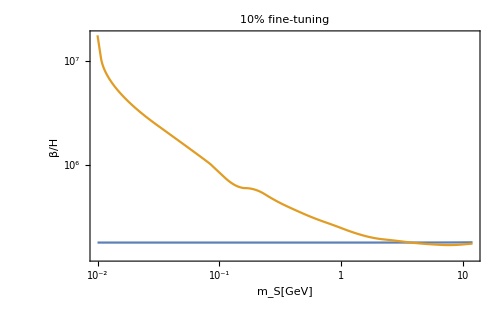

```mathematica
betaH‵curve‵1d={Log10[#1],Log10[#2]}& @@@Import[NotebookDirectory[]<>"phase_transition/output/betaH_inter.csv"];
betaH‵curve‵2d=Drop[{Log10[#1],Log10[#3]}& @@@Import[NotebookDirectory[]<>"phase_transition/output/betaH_inter.csv"],{3,5}];
ListLinePlot[{betaH‵curve‵1d,betaH‵curve‵2d},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["β/H",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},Axes->False,FrameTicks->{{myTicks[5,7,1],None},{myTicks[-3,2,1],None}},PlotRange->Full,InterpolationOrder->2,FrameTicksStyle->{FontSize->18},ImageSize->500,PlotLabel->"10% fine-tuning"]
```

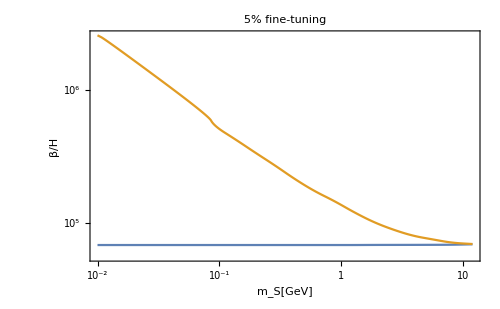

```mathematica
betaH‵curve‵1d2={Log10[#1],Log10[#2]}& @@@Import[NotebookDirectory[]<>"phase_transition/output/betaH_inter_2.csv"];
betaH‵curve‵2d2=Drop[{Log10[#1],Log10[#3]}& @@@Import[NotebookDirectory[]<>"phase_transition/output/betaH_inter_2.csv"],{3,5}];
ListLinePlot[{betaH‵curve‵1d2,betaH‵curve‵2d2},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["β/H",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},Axes->False,FrameTicks->{{myTicks[5,7,1],None},{myTicks[-3,2,1],None}},PlotRange->Full,InterpolationOrder->2,FrameTicksStyle->{FontSize->18},ImageSize->500,PlotLabel->"5% fine-tuning"]
```

## T_n, and strength from T_n

### T_n in log scale

```mathematica
TnCurvedata1d={Log10[#1],#4}& @@@Import[NotebookDirectory[]<>"phase_transition/output/Tcfix_scan.csv"];
TnCurvedata2d={Log10[#1],#5} & @@@Import[NotebookDirectory[]<>"phase_transition/output/Tcfix_scan.csv"];
(*TnCurvedata2d={Log10[#1],#5}& @@@Import[NotebookDirectory[]<>"phase_transition/output/betaH_inter.csv"];
ListPlot[{TnCurvedata1d,TnCurvedata2d}]*)
```

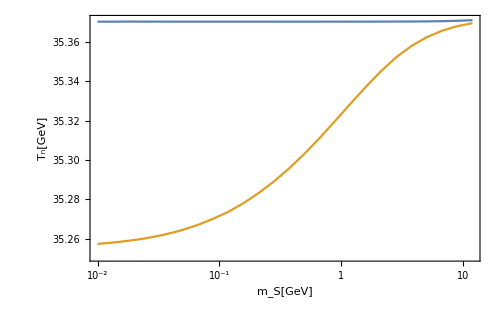

```mathematica
ListLinePlot[{TnCurvedata1d,TnCurvedata2d},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["T_n[GeV]",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},FrameTicks->{{True,None},{myTicks[-3,2,1],None}},Axes->False,ImageSize->500,Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{"1d","2d"}]}],RoundingRadius->5],Scaled[{0.88,0.2}]]}]
```

```mathematica
strengthTnlight1d={Log10[#1],#2,#4}&@@@Import[NotebookDirectory[]<>"phase_transition/output/Tn_bound.csv"];
strengthTnlight2d={Log10[#1],#2,#6}&@@@Import[NotebookDirectory[]<>"phase_transition/output/Tn_bound.csv"];
```

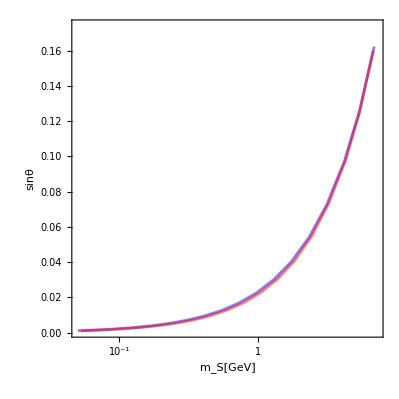

```mathematica
Tn1d=ListContourPlot[{strengthTnlight1d},ContourShading->None,Contours->{1.1},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},FrameTicks->{{True,None},{myTicks[-2,2,1],None}},ContourStyle->Directive[Blue,Thickness[0.005]],PlotRangePadding->None];
Tn2d=ListContourPlot[{strengthTnlight2d},ContourShading->None,Contours->{1.1},ContourStyle->Directive[Red,Thickness[0.005]],PlotRangePadding->None];
Show[{Tn1d,Tn2d},Epilog->{Inset[Framed[Column[{LineLegend[{Blue,Red},{"1d","2d"}]}],RoundingRadius->5],Scaled[{0.13,0.88}]]}]
```

### T_n vs T_c

```mathematica
strengthTndata={#1,#2,#5}&@@@data2d;
```

```mathematica
Tnstrengthfunc[mS_,sinθ_]:=Interpolation[{{#1,#2},#5}& @@@data2d][mS,sinθ]
```

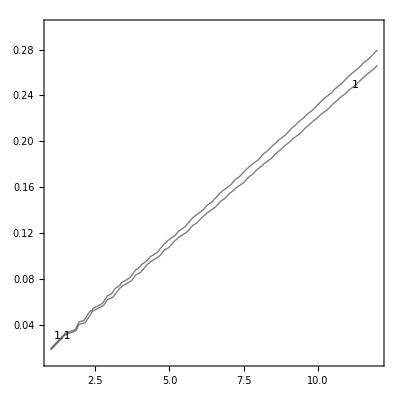

```mathematica
contour = ListContourPlot[strengthTndata,Contours->{1.0,1.1},ContourShading->None,ContourLabels->All]
strengthline=Cases[Normal@contour, Line[x_] :> x, Infinity];
```

```mathematica
bound1[mS_]=Fit[strengthline[[1]],{1,mS^0.5,mS,mS^2},mS];
bound2[mS_]=Fit[strengthline[[2]],{1,mS^0.5,mS,mS^2},mS];
```

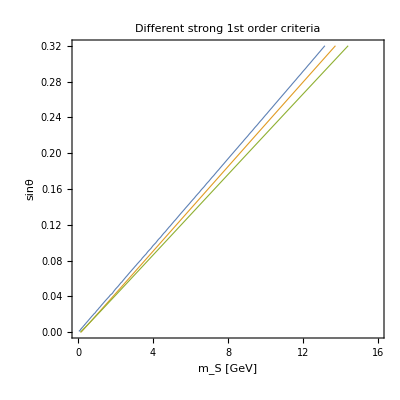

```mathematica
ContourPlot[{strength[mS,sinθ]==1,sinθ==bound1[mS],sinθ==bound2[mS]},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotLabel->"Different strong 1st order criteria",Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2],ColorData[97,3]},{Style["(v(T_c))/T_c=1",FontFamily->"Times",FontSize->18],Style["(v(T_n))/T_n=1.1",FontFamily->"Times",FontSize->18],Style["(v(T_n))/T_n=1",FontFamily->"Times",FontSize->18]}]}],RoundingRadius->5],Scaled[{0.8,0.24}]]},ImageSize->400]
```

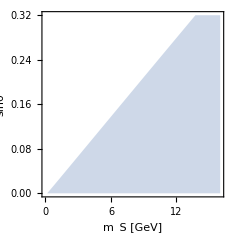

```mathematica
HighT‵Tnuc=RegionPlot[{sinθ<=bound1[mS]},{mS,0,16},{sinθ,0,0.32},BaseStyle->{FontSize->16,FontFamily->"Times"},FrameLabel->{Style["m_S [GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{ColorData[97,1],Opacity[0.3]},BoundaryStyle->None,PlotRangePadding->None]//cleanRegionPlot
```

### Small mass focused: strength

```mathematica
strengthultralightdata={1000*#1,1000*#2,1.24*#4}&@@@Import[NotebookDirectory[]<>"./phase_transition/output/Tn_superlight.csv"]
```

{{1.,0.025412,1.63023},{1.,0.0233322,1.37313},{1.,0.0216416,1.1844},{1.,0.0202292,1.04033},{1.,0.019024,0.92681},{1.54445,0.0392475,1.63023},{1.54445,0.0360354,1.37313},{1.54445,0.0334244,1.1844},{1.54445,0.0312431,1.04033},{1.54445,0.0293817,0.92681},{2.38533,0.0606159,1.63023},{2.38533,0.055655,1.37313},{2.38533,0.0516224,1.1844},{2.38533,0.0482535,1.04033},{2.38533,0.0453786,0.92681},{3.68403,0.0936184,1.63023},{3.68403,0.0859565,1.37313},{3.68403,0.0797283,1.1844},{3.68403,0.0745252,1.04033},{3.68403,0.0700851,0.92681},{5.68981,0.144589,1.63023},{5.68981,0.132756,1.37313},{5.68981,0.123137,1.1844},{5.68981,0.115101,1.04033},{5.68981,0.108243,0.92681},{8.78764,0.223311,1.63023},{8.78764,0.205035,1.37313},{8.78764,0.190179,1.1844},{8.78764,0.177767,1.04033},{8.78764,0.167176,0.92681},{13.5721,0.344893,1.63023},{13.5721,0.316666,1.37313},{13.5721,0.293722,1.1844},{13.5721,0.274553,1.04033},{13.5721,0.258196,0.92681},{20.9614,0.532671,1.63023},{20.9614,0.489076,1.37313},{20.9614,0.453639,1.1844},{20.9614,0.424034,1.04033},{20.9614,0.398771,0.92681},{32.3739,0.822685,1.63023},{32.3739,0.755355,1.37313},{32.3739,0.700624,1.1844},{32.3739,0.6549,1.04033},{32.3739,0.615883,0.92681},{50.,1.2706,1.63023},{50.,1.16661,1.37313},{50.,1.08208,1.1844},{50.,1.01146,1.04033},{50.,0.951201,0.92681}}

```mathematica
strengthultralightdata1d={1000*#1,1000*#2,#4}&@@@Import[NotebookDirectory[]<>"./phase_transition/output/Tn_superlight.csv"];
```

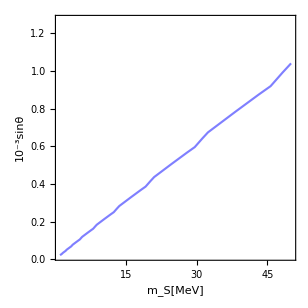

```mathematica
SFOPT‵ultralight=ListContourPlot[strengthultralightdata,Contours->{1.1},ContourShading->None,PlotRange->Full,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^-3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},ContourShading->None,FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},ContourStyle->Directive[Blue,Thickness[0.005]]]
strengthlinelight=Flatten[Cases[Normal@SFOPT‵ultralight, Line[x_] :> x, Infinity],1];
```

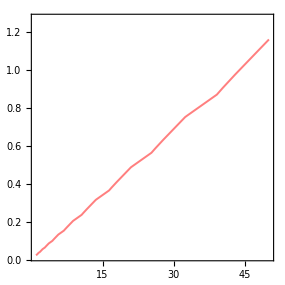

```mathematica
SFOPT‵ultralight‵1d=ListContourPlot[strengthultralightdata1d,ContourShading->None,Contours->{1.1},ContourStyle->Directive[Red,Thickness[0.005]]]
strengthlinelight=Flatten[Cases[Normal@SFOPT‵ultralight, Line[x_] :> x, Infinity],1];
```

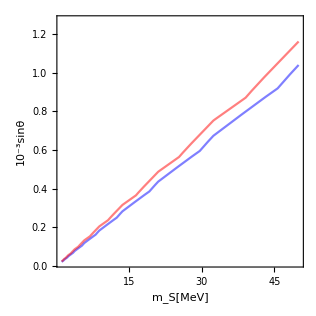

```mathematica
Show[SFOPT‵ultralight,SFOPT‵ultralight‵1d]
```

```mathematica
ultralight‵bound[ϕ_]=Interpolation[strengthlinelight][ϕ]
```

InterpolatingFunction[…][ϕ]

InterpolatingFunction::dmval: Input value {0.00158053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.789475} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

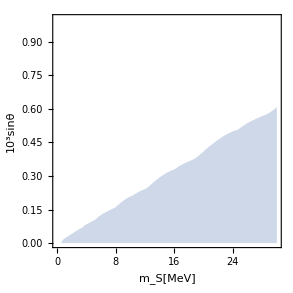

```mathematica
SFOPT‵ultralight‵plot=RegionPlot[ultralight‵bound[mS]>=s,{mS,0,30},{s,0,1},PlotRangePadding->None,PlotStyle->Directive[ColorData[97,1],Opacity[0.3]],BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]}]//cleanRegionPlot
```

## Combine

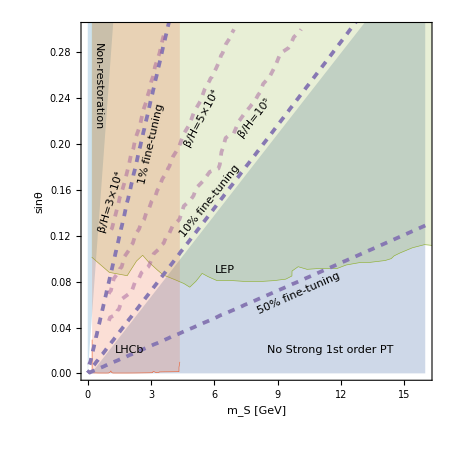

```mathematica
Combine1=Show[HighT‵Tnuc,non‵restore‵plot,LEP1996,LHCb,finetuning,betaH2d,Epilog->{Inset[Framed[Style["No Strong 1st order PT",ColorData[97,"ColorList"][[1]]],FrameStyle->None],{11.5,0.02}],Inset[Framed[Style["LEP",ColorData[97,"ColorList"][[3]]],FrameStyle->None],{6.5,0.09}],Inset[Framed[Style["LHCb",ColorData[97,"ColorList"][[4]]],FrameStyle->None],{2,0.02}],Inset[Rotate[Framed[Style["50% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],24Degree],{10,0.07}],Inset[Rotate[Framed[Style["10% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],51.5Degree],{5.8,0.15}],Inset[Rotate[Framed[Style["1% fine-tuning",ColorData[97,"ColorList"][[5]]],FrameStyle->None],77Degree],{3.,0.2}],Inset[Rotate[Framed[Style["Non-restoration",ColorData[97,7]],FrameStyle->None],-90 Degree],{0.5,0.25}],Inset[Rotate[Framed[Style["β/H=10^5",ColorData[97,9]],FrameStyle->None],52Degree],{7.9,0.223}],Inset[Rotate[Framed[Style["β/H=5×10^4",ColorData[97,9]],FrameStyle->None],62Degree],{5.4,0.223}],Inset[Rotate[Framed[Style["β/H=3×10^4",ColorData[97,9]],FrameStyle->None],73Degree],{1.1,0.15}]},ImageSize->450,Background->White,Axes->None,PlotRange->{{0,16},{0,0.3}}]
Export["/Users/isaac/Dropbox/Research_Project/2022-1-SFOPT_light_singlet/01-Draft/Figures/Combine.pdf",Combine1];
```

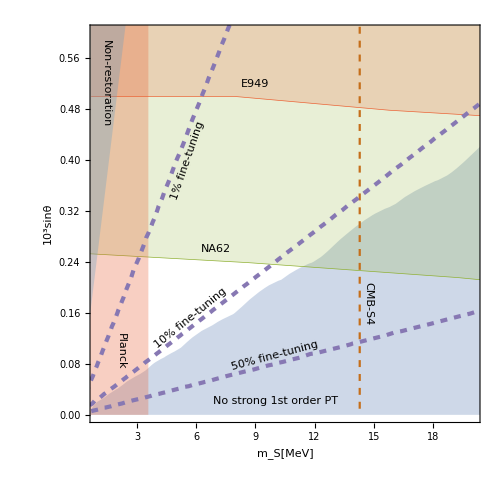

```mathematica
Combine2=Show[{SFOPT‵ultralight‵plot,Kaondecay,Planck,CMB,finetuningsmallmS,non‵restore‵plot‵smallmS},PlotRange->{{1,20},{0,0.6}},ImageSize->500,Epilog->{Inset[Framed[Style["No strong 1st order PT",FontFamily->"Times",FontSize->18,ColorData[97,1]],FrameStyle->None],{10,0.022}],Inset[Framed[Style["NA62",FontFamily->"Times",FontSize->18,ColorData[97,3]],FrameStyle->None],{7,0.26}],Inset[Framed[Style["E949",FontFamily->"Times",FontSize->18,ColorData[97,2]],FrameStyle->None],{9,0.52}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,6]],FrameStyle->None],-90 Degree],{14.7,0.175}],Inset[Rotate[Framed[Style["Planck",ColorData[97,4]],FrameStyle->None],-90 Degree],{2.2,0.1}],Inset[Rotate[Framed[Style["50% fine-tuning",ColorData[97,5]],FrameStyle->None],15Degree],{10,0.093}],Inset[Rotate[Framed[Style["10% fine-tuning",ColorData[97,5]],FrameStyle->None],39Degree],{5.7,0.152}],Inset[Rotate[Framed[Style["1% fine-tuning",ColorData[97,5]],FrameStyle->None],71Degree],{5.55,0.4}],Inset[Rotate[Framed[Style["Non-restoration",ColorData[97,7]],FrameStyle->None],-90 Degree],{1.42,0.52}]}]
Export["/Users/isaac/Dropbox/Research_Project/2022-1-SFOPT_light_singlet/01-Draft/Figures/Combine2.pdf",Combine2];
```